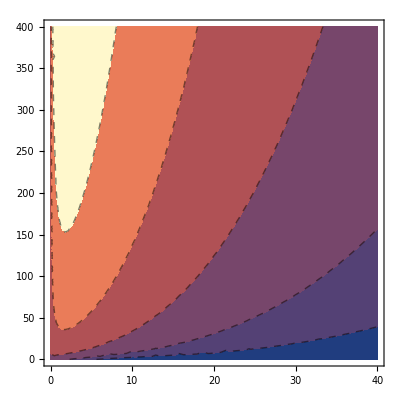

```mathematica
Clear[σf,σ0,χ0μ02σ02,Rcτ]
σ0=1;
μ0=1;
σf=Sqrt[(σ0^2+0.173 χ0μ02σ02 σ0^2/μ0^2 Rcτ)/(1+0.178 Rcτ)^4];
ContourPlot[σf/σ0,{Rcτ,0,40},{χ0μ02σ02,0,400},Contours->{4,2,1,0.5,0.25},ContourStyle->Dashed]
```

## Moments

```mathematica
Clear[y,n,χ,integrand,int]
integrand=((n+1)y^n (8+12χ y +9χ^2 y^2)BesselK[2/3,y])/(2+3χ y)^(n+3)-(y^(n+1)BesselK[1/3,y])/(2+3χ y)^(n+1)
int=Integrate[integrand,{y,0,∞}]//Normal
```

-y^(1+n) (2+3 y χ)^(-1-n) BesselK[1/3,y]+(1+n) y^n (2+3 y χ)^(-3-n) (8+12 y χ+9 y^2 χ^2) BesselK[2/3,y]

1/(3080 Gamma[3+n])3^(-5-n) χ^(-4-n) (30800 3^(2/3) (1+n) χ^(11/3) Gamma[-1/3]^2 Gamma[1/3+n] HypergeometricPFQ[{1/6+n/2,2/3+n/2},{-5/6,-1/3,1/3},1/(9 χ^2)]+18480 3^(2/3) (1+n) χ^(11/3) Gamma[-1/3]^2 Gamma[4/3+n] HypergeometricPFQ[{2/3+n/2,7/6+n/2},{-1/3,1/6,1/3},1/(9 χ^2)]-9240 2^(1/3) 3^(5/6) √π χ^(7/3) Gamma[1/6] Gamma[5/3+n] HypergeometricPFQ[{5/6+n/2,4/3+n/2},{-1/6,1/3,2/3},1/(9 χ^2)]+83160 3^(1/3) (1+n) χ^(7/3) Gamma[-2/3] Gamma[4/3] Gamma[5/3+n] HypergeometricPFQ[{5/6+n/2,4/3+n/2},{-1/6,1/3,5/3},1/(9 χ^2)]+124740 2^(2/3) 3^(1/6) (1+n) √π χ^(11/3) Gamma[5/6] Gamma[7/3+n] HypergeometricPFQ[{7/6+n/2,5/3+n/2},{1/6,1/3,2/3},1/(9 χ^2)]+9240 3^(2/3) χ^(5/3) Gamma[-1/3]^2 Gamma[7/3+n] HypergeometricPFQ[{7/6+n/2,5/3+n/2},{1/6,2/3,4/3},1/(9 χ^2)]-55440 2^(1/3) 3^(5/6) √π χ^(7/3) Gamma[1/6] Gamma[8/3+n] HypergeometricPFQ[{4/3+n/2,11/6+n/2},{1/3,2/3,5/6},1/(9 χ^2)]-55440 3^(1/3) (1+n) χ^(7/3) Gamma[-2/3]^2 Gamma[8/3+n] HypergeometricPFQ[{4/3+n/2,11/6+n/2},{1/3,5/6,5/3},1/(9 χ^2)]-124740 √3 (1+n) π χ^3 Gamma[3+n] HypergeometricPFQ[{3/2+n/2,2+n/2},{1/2,2/3,4/3},1/(9 χ^2)]-55440 3^(2/3) χ^(5/3) Gamma[-1/3]^2 Gamma[10/3+n] HypergeometricPFQ[{5/3+n/2,13/6+n/2},{2/3,7/6,4/3},1/(9 χ^2)]+55440 3^(1/3) χ^(7/3) Gamma[-2/3]^2 Gamma[11/3+n] HypergeometricPFQ[{11/6+n/2,7/3+n/2},{2/3,5/6,4/3},1/(9 χ^2)]+31185 2^(1/3) 3^(5/6) (1+n) √π χ^(7/3) Gamma[1/6] Gamma[11/3+n] HypergeometricPFQ[{11/6+n/2,7/3+n/2},{5/6,4/3,5/3},1/(9 χ^2)]-83160 √3 π χ^2 Gamma[3+n] (χ HypergeometricPFQ[{3/2+n/2,2+n/2},{1/3,1/2,2/3},1/(9 χ^2)]+2 √3 (3+n) HypergeometricPFQ[{2+n/2,5/2+n/2},{5/6,7/6,3/2},1/(9 χ^2)])-299376 (1+n) (3+n) π χ^2 Gamma[3+n] HypergeometricPFQ[{2+n/2,5/2+n/2},{7/6,3/2,11/6},1/(9 χ^2)]+83160 √3 π χ Gamma[3+n] (4 √3 χ HypergeometricPFQ[{3/2+n/2,2+n/2},{1/2,5/6,7/6},1/(9 χ^2)]+(3+n) HypergeometricPFQ[{2+n/2,5/2+n/2},{4/3,3/2,5/3},1/(9 χ^2)])+6237 √3 (1+n) π χ Gamma[3+n] (32 √3 χ HypergeometricPFQ[{3/2+n/2,2+n/2},{1/2,7/6,11/6},1/(9 χ^2)]+5 (3+n) HypergeometricPFQ[{2+n/2,5/2+n/2},{3/2,5/3,7/3},1/(9 χ^2)])-1188 √3 π Gamma[3+n] (35 χ HypergeometricPFQ[{3/2+n/2,2+n/2},{1/2,4/3,5/3},1/(9 χ^2)]+16 √3 (3+n) HypergeometricPFQ[{2+n/2,5/2+n/2},{3/2,11/6,13/6},1/(9 χ^2)])-81 √3 (1+n) π Gamma[3+n] (385 χ HypergeometricPFQ[{3/2+n/2,2+n/2},{1/2,5/3,7/3},1/(9 χ^2)]+128 √3 (3+n) HypergeometricPFQ[{2+n/2,5/2+n/2},{3/2,13/6,17/6},1/(9 χ^2)])+187110 2^(2/3) 3^(1/6) √π χ^(5/3) Gamma[5/6] Gamma[13/3+n] HypergeometricPFQ[{13/6+n/2,8/3+n/2},{7/6,4/3,5/3},1/(9 χ^2)])

```mathematica
(* low χ asymptotics *)
lowχ= 2/(Gamma[n/2+1/6]Gamma[n/2+11/6])Series[int,{χ,0,2}]//Normal//Simplify;
(*lowχ=lowχ//FullSimplify;*)
eq8=1-(3(n+1)Gamma[n/2+2/3]Gamma[n/2+7/3])/(Gamma[n/2+1/6]Gamma[n/2+11/6])χ+((n+1)(3n+1)(28+n(3n+17)))/8 χ^2;
lowχ/eq8//FullSimplify
```

(ⅈ^Floor[Arg[χ]/π] 2^(2+n) 3^(-11/2-2 n) ⅇ^(-(2 (-1)^Floor[Arg[χ]/π])/(3 χ)+ⅈ n π Floor[Arg[χ]/π]) π^(3/2) χ^(-7/2-2 n) (-3 ⅈ ⅇ^(ⅈ n π) (-16+(149+36 n (7+2 n)) χ)+(-1)^(1+Floor[Arg[χ]/π]) ⅇ^((4 (-1)^Floor[Arg[χ]/π])/(3 χ)) (-144+(77+36 n (5+2 n)) χ+9 (1+n) (-79+36 n (3+2 n)) χ^2+(-1)^Floor[Arg[χ]/π] (-48+3 (149+36 n (7+2 n)) χ))+ⅈ ⅇ^(ⅈ π (n+Ceiling[-Arg[χ]/π])) (-144+χ (77-711 χ+9 n (20+29 χ+4 n (2+9 (5+2 n) χ))))))/(((8+(1+n) (1+3 n) (28+n (17+3 n)) χ^2) Gamma[1/6+n/2] Gamma[11/6+n/2]-24 (1+n) χ Gamma[2/3+n/2] Gamma[7/3+n/2]) Gamma[3+n])

```mathematica
(Refine[lowχ//Simplify,{χ>0}]//.{ⅇ^(ⅈ n π)->(-1)^(n)})//FullSimplify
```

(2^(-1+n) 3^(-11/2-2 n) ⅇ^(-2/3/χ) π^(3/2) χ^(-7/2-2 n) (ⅈ ⅇ^(ⅈ n π) (-96-2 (185+72 n (4+n)) χ+9 (1+n) (-79+36 n (3+2 n)) χ^2)+ⅇ^(4/3/χ) (192-χ (524+72 n (13+4 n)+9 (1+n) (-79+36 n (3+2 n)) χ))))/(Gamma[1/6+n/2] Gamma[11/6+n/2] Gamma[3+n])

```mathematica
lowχ=%;
res=lowχ-eq8;
Refine[res,{χ>0,n>0}]//Simplify
```

-1-1/8 (1+n) (1+3 n) (28+n (17+3 n)) χ^2+(3 (1+n) χ Gamma[2/3+n/2] Gamma[7/3+n/2])/(Gamma[1/6+n/2] Gamma[11/6+n/2])+(2^(-1+n) 3^(-11/2-2 n) ⅇ^(-2/3/χ) π^(3/2) χ^(-7/2-2 n) (ⅈ ⅇ^(ⅈ n π) (-96-2 (185+72 n (4+n)) χ+9 (1+n) (-79+36 n (3+2 n)) χ^2)+ⅇ^(4/3/χ) (192-χ (524+72 n (13+4 n)+9 (1+n) (-79+36 n (3+2 n)) χ))))/(Gamma[1/6+n/2] Gamma[11/6+n/2] Gamma[3+n])

-1-1/8 (1+n) (1+3 n) (28+n (17+3 n)) χ^2+(3 (1+n) χ Gamma[2/3+n/2] Gamma[7/3+n/2])/(Gamma[1/6+n/2] Gamma[11/6+n/2])+(ⅈ^n 3^(-11/2-2 n) ⅇ^(-(4+3 ⅈ n π χ)/(6 χ)) χ^(-7/2-2 n) (3080 (1/2 (ⅈ+√3) ⅇ^(ⅈ n π) (-48+(77+180 n+72 n^2) χ)+ⅇ^(4/3/χ) (48+(77+180 n+72 n^2) χ)) Gamma[-1/3]^2 Gamma[1/3] Gamma[2/3] Gamma[7/6] Gamma[2+n/2] Gamma[13/6+n/2] Gamma[8/3+n/2] Gamma[7/3+n] Gamma[(3+n)/2] Gamma[(5+n)/2]+3 Gamma[7/6+n/2] (-3080 (1/2 (ⅈ+√3) ⅇ^(ⅈ n π) (-48+(221+252 n+72 n^2) χ)+ⅇ^(4/3/χ) (48+(221+252 n+72 n^2) χ)) Gamma[-1/3]^2 Gamma[2/3] Gamma[7/6] Gamma[4/3] Gamma[2+n/2] Gamma[8/3+n/2] Gamma[(3+n)/2] Gamma[10/3+n] Gamma[(5+n)/2]+3 √π Gamma[5/3+n/2] (1/2^(1/3)1155 √3 ((ⅈ+√3) ⅇ^(ⅈ n π) (-48+(365+324 n+72 n^2) χ)+2 ⅇ^(4/3/χ) (48+(365+324 n+72 n^2) χ)) Gamma[5/6] Gamma[7/6] Gamma[4/3] Gamma[5/3] Gamma[2+n/2] Gamma[(3+n)/2] Gamma[13/3+n] Gamma[(5+n)/2]+2 π Gamma[13/6+n/2] Gamma[8/3+n/2] Gamma[3+n] (-6 (3+n) (-616 ⅈ ⅇ^(ⅈ n π) (5 √3 Gamma[4/3] Gamma[5/3]-18 (1+n) χ Gamma[7/6] Gamma[11/6])-616 ⅇ^(4/3/χ) (5 √3 Gamma[4/3] Gamma[5/3]-18 (1+n) χ Gamma[7/6] Gamma[11/6])+33 ⅇ^(4/3/χ) (192 Gamma[11/6] Gamma[13/6]+χ (308 Gamma[11/6] Gamma[13/6]+720 n Gamma[11/6] Gamma[13/6]+288 n^2 Gamma[11/6] Gamma[13/6]-105 √3 Gamma[5/3] Gamma[7/3]-105 √3 n Gamma[5/3] Gamma[7/3]))+33 ⅈ ⅇ^(ⅈ n π) (-192 Gamma[11/6] Gamma[13/6]+χ (308 Gamma[11/6] Gamma[13/6]+720 n Gamma[11/6] Gamma[13/6]+288 n^2 Gamma[11/6] Gamma[13/6]+105 √3 Gamma[5/3] Gamma[7/3]+105 √3 n Gamma[5/3] Gamma[7/3]))-216 ⅈ ⅇ^(ⅈ n π) (1+n) χ (-48+(-79+108 n+72 n^2) χ) Gamma[13/6] Gamma[17/6]+216 ⅇ^(4/3/χ) (1+n) χ (48+(-79+108 n+72 n^2) χ) Gamma[13/6] Gamma[17/6]) Gamma[(3+n)/2]+77 (-1920 ⅈ ⅇ^(ⅈ n π) Gamma[5/6] Gamma[7/6]+1920 ⅇ^(4/3/χ) Gamma[5/6] Gamma[7/6]+5 ⅈ √3 ⅇ^(ⅈ n π) (-48+(77+180 n+72 n^2) χ) Gamma[4/3] Gamma[5/3]-5 √3 ⅇ^(4/3/χ) (48+(77+180 n+72 n^2) χ) Gamma[4/3] Gamma[5/3]+3456 ⅈ ⅇ^(ⅈ n π) (1+n) χ Gamma[7/6] Gamma[11/6]+3456 ⅇ^(4/3/χ) (1+n) χ Gamma[7/6] Gamma[11/6]+540 ⅈ √3 ⅇ^(ⅈ n π) (1+n) χ Gamma[5/3] Gamma[7/3]-540 √3 ⅇ^(4/3/χ) (1+n) χ Gamma[5/3] Gamma[7/3]) Gamma[(5+n)/2])))))/(24640 √π Gamma[1/6+n/2] Gamma[7/6+n/2] Gamma[5/3+n/2] Gamma[11/6+n/2] Gamma[2+n/2] Gamma[13/6+n/2] Gamma[8/3+n/2] Gamma[(3+n)/2] Gamma[3+n] Gamma[(5+n)/2])

```mathematica
(* high χ asymptotics *)
highχ= 2/(Gamma[n/2+1/6]Gamma[n/2+11/6]) Asymptotic[int,χ->∞]//FullSimplify;
highχ=Asymptotic[highχ,χ->∞]//Normal//Simplify;
(* confirm it gives same result as equation 9 *)
eq9=-((n+1)(28+9n(n+3))Gamma[-1/3]Gamma[2/3]Gamma[n+1/3])/(27Gamma[n/2+1/6]Gamma[n/2+11/6]Gamma[n+3])(3χ)^(-n-1/3);
highχ/eq9//FullSimplify
```

1